InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>]

-Graphics3D-

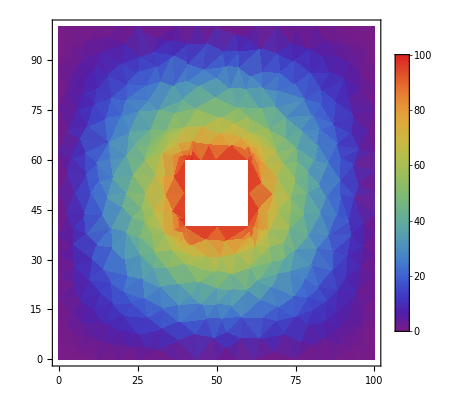

```mathematica
Ω=RegionDifference[Rectangle[{0,0},{100,100}],Rectangle[{40,40},{60,60}]];
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,DirichletCondition[u[x,y]==100.,x==40&&40≤y≤60||x==60&&40≤y≤60||40≤x≤60&&y==40||40≤x≤60&&y==60],u[x,0]==u[x,100]==u[0,y]==u[100,y]==0},u,{x,y}∈Ω]

Plot3D[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic]

DensityPlot[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic]
```

```mathematica
sol=NDSolveValue[{D[u[x,y],x,x]+D[u[x,y],y,y]==0,DirichletCondition[u[x,y]==100.,x==40&&40≤y≤60||x==60&&40≤y≤60||40≤x≤60&&y==40||40≤x≤60&&y==60],u[x,0]==u[x,100]==u[0,y]==u[100,y]==0},u,{x,y}∈Ω,Method->{"FiniteElement","MeshOptions"->{"BoundaryMeshGenerator"->"Continuation"}}]

Plot3D[sol[x,y],{x,y}∈Ω,Mesh->None,ColorFunction->"Rainbow",PlotRange->All,PlotLegends->Automatic]
```

InterpolatingFunction[{{0., 100.}, {0., 100.}}, <>]

-Graphics3D-

## Első rendű PDE szimbolikusan

#### Partial differential equation with boundary condition

```mathematica
DSolve[{D[u[x,y],x]+D[u[x,y],y]==u[x,y]+x^2,u[0,y]==Sin[y]+y^2},u,{x,y}]
```

{{u→Function[{x,y},-2+2 ⅇ^x-2 x-x^2+ⅇ^x x^2-2 ⅇ^x x y+ⅇ^x y^2-ⅇ^x Sin[x-y]]}}

#### Partial differential equation without boundary condition (more complex)

```mathematica
DSolve[{Sin[x] D[u[x,y],x]+y D[u[x,y],y]==u[x,y]+x^2},u,{x,y}]
```

{{u→Function[{x,y},-x^2-ⅈ x^2 Tan[x/2]+4 x Log[1-ⅇ^(ⅈ x)] Tan[x/2]-4 ⅈ PolyLog[2,ⅇ^(ⅈ x)] Tan[x/2]+Tan[x/2] C[1][y Cot[x/2]]]}}

#### Partial integral equation

```mathematica
sol=DSolve[{u[x,y]Integrate[u[x,y],x]+Integrate[u[x,y],y]*Sin[x]*x==(1+x^2)u[x,y]/x^2+y^2},u,{x,y}]
```

{{u→Function[{x,y},(1+1/x^2-x y Sin[x]-√(4 x y^2+(-1-1/x^2+x y Sin[x])^2))/(2 x)]},{u→Function[{x,y},(1+1/x^2-x y Sin[x]+√(4 x y^2+(-1-1/x^2+x y Sin[x])^2))/(2 x)]}}

```mathematica
u[x,y]/.sol[[1]]
Plot3D[u[x,y]/.sol[[1]],{x,0.01,8Pi},{y,0,10}]
```

(1+1/x^2-x y Sin[x]-√(4 x y^2+(-1-1/x^2+x y Sin[x])^2))/(2 x)

-Graphics3D-